# Practical 2

## Second Order Ordinary Differential Equations

### Second order ordinary differential equations: The differential equations that involves the second order derivatives of dependent variable with respect to independent variable Command: DSolve[Differential Equation, y[x], x]

### Q1 Solve the following second order ordinary differential equation (d^2 y)/dx^2+ 3 dy/dx+ y = 0

1. Solve y'' (x) + 3y’(x)+y=0

```mathematica
eq1= (y''[x] + 3y'[x] + 2y[x] == 0)
```

2 y[x]+3 y'[x]+y''[x]==0

```mathematica
GS1=DSolve[eq1, y[x], x]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^-x C[2]}}

2. Solve the above differential equation using the initial conditions given as
y(0)= 1 and y’(0)= 5

```mathematica
PS1 = Evaluate[y[x]/.GS1[[1]]/.{C[1]->1, C[2]->5} ]
```

ⅇ^(-2 x)+5 ⅇ^-x

3. Solve the above differential equation using the initial conditions given as
y(0)= 1, 2, -1 and y’(0)= 5, 4, 6 and plot the graphs

```mathematica
PSX1 = Evaluate[y[x]/.GS1[[1]]/.{C[1]->{1, 2, -1}, C[2]->{5, 4, 6}} ]
```

{ⅇ^(-2 x)+5 ⅇ^-x,2 ⅇ^(-2 x)+4 ⅇ^-x,-ⅇ^(-2 x)+6 ⅇ^-x}

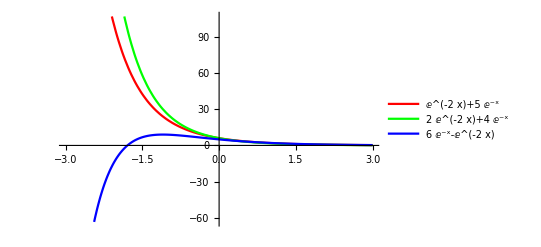

```mathematica
Plot[PSX1, {x, -3, 3}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}}, PlotLegends->PSX1]
```

### Q2 Solve the following second order ordinary differential equation (d^2 y)/dx^2+ y = sec(x)

1. Solve y'' (x) + y(x) = sec(x)

```mathematica
eq2= (y''[x] + y[x] == Sec[x])
```

y[x]+y''[x]==Sec[x]

```mathematica
GS2 = DSolve[eq2, y[x], x]
```

{{y[x]→C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]}}

2. Solve the above differential equation using the initial conditions given as
y(0)= -14, -10, 2 and y’(0)= 4, -1, 3 and plot the graph

```mathematica
PSX2 = Evaluate[y[x]/.GS2[[1]]/.{C[1]->{-14, -10, 2}, C[2]->{4, -1, 3}} ]
```

{-14 Cos[x]+Cos[x] Log[Cos[x]]+4 Sin[x]+x Sin[x],-10 Cos[x]+Cos[x] Log[Cos[x]]-Sin[x]+x Sin[x],2 Cos[x]+Cos[x] Log[Cos[x]]+3 Sin[x]+x Sin[x]}

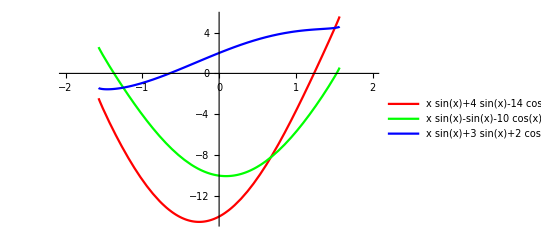

```mathematica
Plot[PSX2, {x, -2, 2}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}}, PlotLegends->PSX2]
```

### Q3 Solve the following second order ordinary differential equation (d^2 y)/dx^2- 6 dy/dx+ 9y = 0

1. Solve y'' (x) - 6y’(x)+9y=0

```mathematica
eq3= (y''[x] - 6y'[x] + 9y[x] == 0)
```

9 y[x]-6 y'[x]+y''[x]==0

```mathematica
GS3=DSolve[eq3, y[x], x]
```

{{y[x]→ⅇ^(3 x) C[1]+ⅇ^(3 x) x C[2]}}

2. Solve the above differential equation using the initial conditions given as
y(0)= 1 and y’(0)= 1

```mathematica
PS3 = Evaluate[y[x]/.GS3[[1]]/.{C[1]->1, C[2]->1} ]
```

ⅇ^(3 x)+ⅇ^(3 x) x

3. Solve the above differential equation using the initial conditions given as
y(0)= 1, 2, -1 and y’(0)= 1, 2, -1 and plot the graphs

```mathematica
PSX3 = Evaluate[y[x]/.GS3[[1]]/.{C[1]->{1, 2, -1}, C[2]->{1, 2, -1}} ]
```

{ⅇ^(3 x)+ⅇ^(3 x) x,2 ⅇ^(3 x)+2 ⅇ^(3 x) x,-ⅇ^(3 x)-ⅇ^(3 x) x}

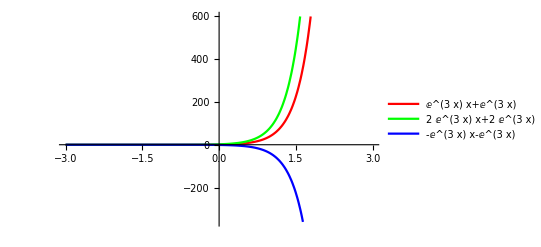

```mathematica
Plot[PSX3, {x, -3, 3}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}}, PlotLegends->PSX3]
```

### Q4 Solve the following second order ordinary differential equation (d^2 y)/dx^2+ 16y = 0

1. Solve y'' (x) - 6y’(x)+9y=0

```mathematica
eq4= (y''[x] + 16y[x] == 0)
```

16 y[x]+y''[x]==0

```mathematica
GS4=DSolve[eq4, y[x], x]
```

{{y[x]→C[1] Cos[4 x]+C[2] Sin[4 x]}}

2. Solve the above differential equation using the initial conditions given as
y(0)= 1 and y’(0)= 1

```mathematica
PS4 = Evaluate[y[x]/.GS4[[1]]/.{C[1]->-10, C[2]->3} ]
```

-10 Cos[4 x]+3 Sin[4 x]

3. Solve the above differential equation using the initial conditions given as
y(0)= -1, 1, 1, -1 and y’(0)= 1, -1, 1, -1 and plot the graphs

```mathematica
PSX4 = Evaluate[y[x]/.GS4[[1]]/.{C[1]->{-1, 1, 1, -1}, C[2]->{1, -1, 1, -1}} ]
```

{-Cos[4 x]+Sin[4 x],Cos[4 x]-Sin[4 x],Cos[4 x]+Sin[4 x],-Cos[4 x]-Sin[4 x]}

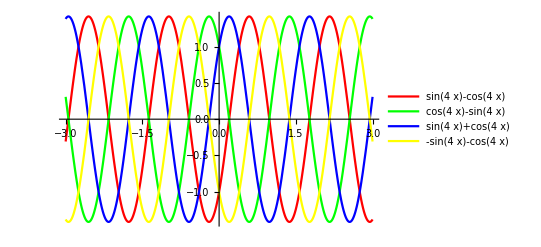

```mathematica
Plot[PSX4, {x, -3, 3}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}, {Yellow, Thick}}, PlotLegends->PSX4]
```

### Q5 Solve the following second order ordinary differential equation 4(d^2 y)/dx^2+ 24 dy/dx+ 37y = 0

1. Solve 4y'' (x) + 24y’(x)+37y=0

```mathematica
eq5= (4y''[x] + 24y'[x] + 37y[x] == 0)
```

37 y[x]+24 y'[x]+4 y''[x]==0

```mathematica
GS5=DSolve[eq5, y[x], x]
```

{{y[x]→ⅇ^(-3 x) C[2] Cos[x/2]+ⅇ^(-3 x) C[1] Sin[x/2]}}

2. Solve the above differential equation using the initial conditions given as
y(0)= 1 and y’(0)=0

```mathematica
PS5 = Evaluate[y[x]/.GS5[[1]]/.{C[1]->1, C[2]->0} ]
```

ⅇ^(-3 x) Sin[x/2]

3. Solve the above differential equation using the initial conditions given as
y(0)= 1, 0, 1, -1 and y’(0)= 0, 1, 1, -1 and plot the graphs

```mathematica
PSX5 = Evaluate[y[x]/.GS5[[1]]/.{C[1]->{1, 0, 1, -1}, C[2]->{0, 1, 1, -1}} ]
```

{ⅇ^(-3 x) Sin[x/2],ⅇ^(-3 x) Cos[x/2],ⅇ^(-3 x) Cos[x/2]+ⅇ^(-3 x) Sin[x/2],-ⅇ^(-3 x) Cos[x/2]-ⅇ^(-3 x) Sin[x/2]}

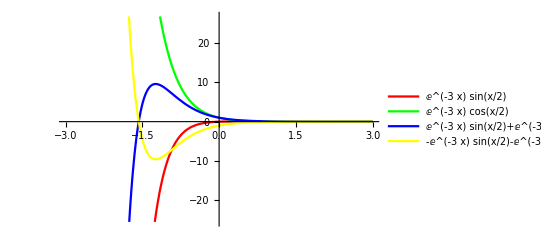

```mathematica
Plot[PSX5, {x, -3, 3}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}, {Yellow, Thick}}, PlotLegends->PSX5]
```